Initial Graph:

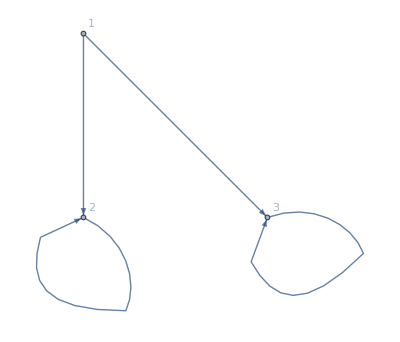

Frequency Vector: {{{1,γ/(1-γ),0},{1,0,γ/(1-γ)}},{{0,1/(1-γ),0}},{{0,0,1/(1-γ)}}}

#############################################################################################

Equation List: {r[1]+(γ r[2])/(1-γ),r[1]+(γ r[3])/(1-γ)}

Non-Dominated Equation List: {r[1]+(γ r[2])/(1-γ),r[1]+(γ r[3])/(1-γ)}

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 1

Inequalities used: r[3]<r[2]

Average Optimal Value: (3+γ)/(12-12 γ)

Power: 7/12-1/(4 γ)

Measure: 1/2

Power/Measure: 7/6-1/(2 γ)

Variance: 1/12 (2+γ^2)

γ=1: 1/3 Cumulative Sum: 1/3

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 2

Inequalities used: r[3]>r[2]

Average Optimal Value: (3+γ)/(12-12 γ)

Power: 7/12-1/(4 γ)

Measure: 1/2

Power/Measure: 7/6-1/(2 γ)

Variance: 1/12 (2+γ^2)

γ=1: 1/3 Cumulative Sum: 2/3

#############################################################################################

Equation List: {r[2]/(1-γ)}

#############################################################################################

Equation List: {r[3]/(1-γ)}

=================================================

Final Variance: 1/36 (3-6 γ+5 γ^2)

Final Power: -1/(2 (-1+γ))

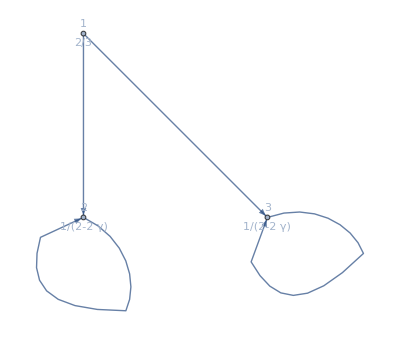

```mathematica
(*Be sure to run "runThisFileFirst.nb" firsts*)
(*To Run, press Shift+Enter. Or, at top, Evaluation -> Evaluate Cells*)
(*Note: If running forever,(usually #states > 7), then Evaluation -> Quit Kernal -> local*)

(*Indexing of graphs start with "1", cannot use 0 or other letters/numbers*)
vertexAndNodes = {1->2, 2->2, 1->3, 3->3};

(*            graph    , First/All, OnlyPower/Basic/Measure*)
powerOfGraph[vertexAndNodes, "All", "Basic"]

(*
First - calculate Power for first state only;
All - Calcuate Power for all states;
OnlyPower - Display only final power graph;
Basic - Display basic info such as frequency vector, non-dominated equations, and integrations;
Measure - Display Measure and power graph. Only works with "First";
*)
```